# DISSERTAÇÃO DE MESTRADO CABO UMBILICAL DA PETROBRÁS

## Aluno: Paulo Eduardo Darski Rocha Profs.: Dr. Antonio Carlos Siqueira de Lima / PhD Sandoval Carneiro Jr. Poli/COPPE/UFRJ

## Opções de programa

```mathematica
Clear["Global`*"]
```

```mathematica
SetOptions[{ListPlot,ListLogLinearPlot,ListLogLogPlot},Axes->False,Frame->True,Joined->True,ImageSize->450,PlotStyle->{PointSize[0.015]},BaseStyle->{14,FontFamily->"Helvetica"}];
```

```mathematica
plstyle1={AbsoluteThickness[1],RGBColor[1,0,0]}; (*vermelho*)
plstyle2={AbsoluteThickness[1],RGBColor[0,0,1]};  (*azul*)
plstyle3={AbsoluteThickness[1],Hue[.4],Dashing[{.02}]};  (*verde pontilhado*)
plstyle4={AbsoluteThickness[1],RGBColor[0,0,1],Dashing[{.02}]};  (*azul pontilhado*)
plstyle5={AbsoluteThickness[1],RGBColor[0,0.5,0]}; (*verde claro*)
plstyle6={AbsoluteThickness[1],RGBColor[0,0,0],Dashing[{.02}]};  (*preto*)
plstyle7={AbsoluteThickness[1],{GrayLevel[0.8]}};  (*cinza*)
plstyle8={AbsoluteThickness[1],RGBColor[0.5,0.5,0.5]};(*marrom*)
plstyle9={AbsoluteThickness[1],Hue[.4],Dashing[{.02}]};  (*verde pontilhado*)
```

## Dados de Entrada

### DADOS DO PIPE TYPE INTERNO

#### RAIOS DOS CABOS COAXIAIS DO CIRCUITO DE FORÇA

```mathematica
r0=0;
r1=9.15 10^-3;
r2=r1+( 0.7 10^-3+ 5.5 10^-3);
r3=r2+( 0.7 10^-3+(0.2 10^-3+0.1 0.2 10^-3)+(0.127 10^-3+0.25  0.127 10^-3));
r4=r3+1.5 10^-3;
DiametroSC=N[r4*2 10^3]
```

35.8575

```mathematica
ncx=2 (*número de elementos metálicos*)
```

2

#### CONSTANTES ELÉTRICAS DOS CABOS COAXIAIS DO CIRCUITO DE FORÇA

```mathematica
μ=4.0 π 10^-7;
ϵ=8.854*10^-12;
```

```mathematica
ρc=1.7241 10^-8;
ρs=1.7241 10^-8;
μc=1;
μs=1;
ϵc=3.0; (*EPR*)
ϵs=3.72; (*PE*)
```

#### RAIOS DOS CABOS DE FIBRA ÓPTICA;

```mathematica
r5=12.1 .5 10^-3;
r6=r5+.8 10^-3 ;
r7=17.1 .5 10^-3;
DiametroFO=N[r7*2 10^3]
```

17.1

```mathematica
nfo=1(*número de elementos metálicos*)
```

1

#### CONSTANTES ELÉTRICAS DOS CABOS DE FIBRA ÓPTICA;

```mathematica
ρf=1.7241 10^-8;
μf=1;
ϵf=2.3;  (*PET*)
```

#### ANGULO ENTRE OS ELEMENTOS CONDUTORES;

```mathematica
θjk=(2 π)/3; (*entre os cabos coaxias*)
θlm=θjk; (*entre os cabos de fibra optica*)
θjl=(1 π)/3; (*entre os cabos coaxias e de fibra optica*)
θjm=π; (*entre os cabos coaxias e de fibra optica*)
```

```mathematica
b=Sqrt[(2 r4)^2/(2-2 Cos[θjk])];
b2=NSolve[c^2-(2(b) Cos[(1 π)/3])*c+((b)^2)-((r4+r7)^2)==0,c];
b3=b2[[1,1,1]]/.%;
Dj=b; (*distancia do cabo ao centro do PT*)
Dk=Dj;(*distancia do cabo ao centro do PT*)
Dl=b3[[2]]; (*distancia do cabo ao centro do PT*)
Dm=Dl;(*distancia do cabo ao centro do PT*)
```

#### RAIOS DAS CAMADAS METÁLICAS;

```mathematica
rp1=b+r4;
rp2=rp1+.8 10^-3;
rp3=rp2+ 4  10^-3;
DiametroPTi=N[rp3*2 10^3]
```

86.8622

```mathematica
npt1=2;(*número de elementos metálicos*)
```

#### CONSTANTES ELÉTRICAS DAS CAMADAS METÁLICAS;

```mathematica
ρp=0.171 10^-6;
μp=200;
ϵp1=3.0; (*EPR*)
ϵp2=2.3; (*HDPE*)
```

### DADOS DA TUBULAÇÃO H5

#### RAIOS DAS TUBULAÇÕES;

```mathematica
rh53=1.0395 .5 25.4 10^-3;
rh52=rh53 -(rh53/3);
rh51=rh52-(2 10^-3);
DiametroRH5=N[rh53*2 10^3]
```

26.4033

```mathematica
nh5=1(*número de elementos metálicos*)
```

1

#### ANGULO ENTRE OS ELEMENTOS CONDUTORES;

```mathematica
θhh=(2 π)/3; (*entre os h5*)
```

#### CONSTANTES ELÉTRICAS DAS CAMADAS METÁLICAS;

```mathematica
ρh5=0.2 10^-6;
μh5=200;
ϵh5=2.4;  (*XLPE*)
```

### DADOS DO CABO

#### RAIOS DAS TUBULAÇÕES;

```mathematica
rp4=rp3+DiametroRH5 10^-3;
rp5=rp4+5.8 10^-3;
rp6=rp5+12 10^-3;
rp7=rp6+5 10^-3;
DiametroPTi=N[rp7*2 10^3]
```

185.269

```mathematica
npt=1;(*número de elementos metálicos*)
θph=(1 π)/6; (*entre o pipe e o h5*)
θhh=(2 π)/3; (*entre o pipe e o h5*)
θpt1=0; (*entre o pipe e o h5*)
Dpt1=0; (*distancia do PT1 ao centro do cabo*)
Dh5=rp3+rh53;(*distancia do cabo ao centro do PT*)
```

#### CONSTANTES ELÉTRICAS DAS CAMADAS METÁLICAS;

```mathematica
ρa=0.171 10^-6;
μa=400;
ϵp3=2.3; (*HDPE*)
ϵp4=2.3; (*HDPE*)
ϵp5=2.3; (*HDPE*)
```

### DADOS DA REDE

```mathematica
compr=10*10^3;
h=100;
ρg=0.2;
μg=1;
```

```mathematica
ncond=3 ncx+3 nfo+npt1; (*número de elementos metálicos*)
```

## Configuração da Rede

### LOCALIZAÇÃO DOS CONDUTORES NO CIRCUITO DE FORÇA

#### CABOS COAXIAIS

```mathematica
xc1=0;yc1=Dj ;
xc2=Dk Sin[Pi/3];yc2=-Dk Sin[Pi/6];
xc3=-Dk  Sin[Pi/3];yc3=-Dk Sin[Pi/6];
```

#### FIBRA ÓPTICA

```mathematica
xc4=-Dl Sin[Pi/3];yc4=Dl Sin[Pi/6] ;
xc5=Dl Sin[Pi/3];yc5=Dl Sin[Pi/6];
xc6=0;yc6=-Dl;
```

#### TUBO

```mathematica
xpt=0;
ypt=0;
```

#### H5

```mathematica
xc7=-Dh5 Sin[Pi/3];yc7=Dh5 Sin[Pi/6] ;
xc8=Dh5 Sin[Pi/3];yc8=Dh5 Sin[Pi/6];
xc9=0;yc9=-Dh5;
```

#### LAYOUT DO PT INTERNO

```mathematica
xc={xc1,xc1,xc1,xc1,xc2,xc2,xc2,xc2,xc3,xc3,xc3,xc3,xc4,xc4,xc4,xc5,xc5,xc5,xc6,xc6,xc6,xpt,xpt,xpt};
yc={yc1,yc1,yc1,yc1,yc2,yc2,yc2,yc2,yc3,yc3,yc3,yc3,yc4,yc4,yc4,yc5,yc5,yc5,yc6,yc6,yc6,ypt,ypt,ypt};
r={r1,r2,r3,r4,r1,r2,r3,r4,r1,r2,r3,r4,r5,r6,r7,r5,r6,r7,r5,r6,r7,rp1,rp2,rp3};
```

```mathematica
pipeinterno=Table[{Circle[{xc[[i]],yc[[i]]},r[[i]]]},{i,1,Length[xc]}];
```

#### LAYOUT DO CABO

```mathematica
xcp={xc1,xc1,xc1,xc1,xc2,xc2,xc2,xc2,xc3,xc3,xc3,xc3,xc4,xc4,xc4,xc5,xc5,xc5,xc6,xc6,xc6,xpt,xpt,xpt,xc7,xc7,xc7,xc8,xc8,xc8,xc9,xc9,xc9,xpt,xpt,xpt,xpt};
ycp={yc1,yc1,yc1,yc1,yc2,yc2,yc2,yc2,yc3,yc3,yc3,yc3,yc4,yc4,yc4,yc5,yc5,yc5,yc6,yc6,yc6,ypt,ypt,ypt,yc7,yc7,yc7,yc8,yc8,yc8,yc9,yc9,yc9,ypt,ypt,ypt,ypt};
rt={r1,r2,r3,r4,r1,r2,r3,r4,r1,r2,r3,r4,r5,r6,r7,r5,r6,r7,r5,r6,r7,rp1,rp2,rp3,rh51,rh52,rh53,rh51,rh52,rh53,rh51,rh52,rh53,rp4,rp5,rp6,rp7};
```

```mathematica
umbilical=Table[{Circle[{xcp[[i]],ycp[[i]]},rt[[i]]]},{i,1,Length[xcp]}];
```

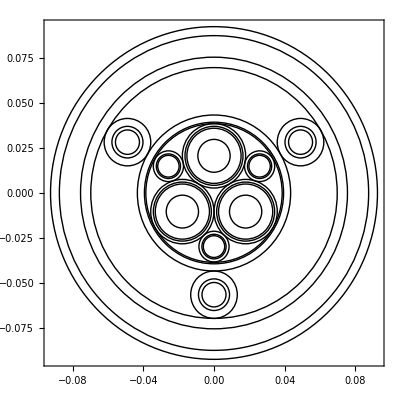

```mathematica
Show[Graphics[umbilical],AspectRatio->Automatic,Axes->False,Frame->True,PlotRange->All]
```

## Freqüências

### FREQUÊNCIA

```mathematica
d1=-1;
d2=6;
freqlog[i_,f_,np_]:=Table[N[10^(i+x(f-i)/(Floor[np]-1))],{x,0,np-1}]
freqlin[i_,f_,np_]:=Table[N[(i+x(f-i)/(Floor[np]-1))],{x,0,np-1}]
(*f0=freqlog[d0,d1,500];*)
f1=freqlog[d1,d2,60];
f2=freqlin[10^d1, 10^d2,60];
f=Sort@Join[f2,f1];
nf=Length[f];
```

### LISTAS

### Inicialização das listas

```mathematica
T=Table[0,{n,1,nf}];
T1=λ=λ0=Γ1=Yc1=Af1=Am1=γm=T;
```

## Impedancia do PT interno

### MATRIX DE IMPEDÂNCIA INTERNA DOS CABOS (Zi)

#### IMPEDÂNCIA INTERNA DO CABO COAXIAL

IMPEDÂNCIAS COMPONENTES;

```mathematica
mc=√((I ω μ μc)/ρc);
ms=√((I ω  μ μs)/ρs);
delta=r3-r2;
sum=r2+r3;
z1=(ρc mc)/(2π r1) Coth[0.777*mc*r1]+(0.356 ρc)/(π r1^2);
z2=(I ω μ)/(2π)Log[r2/r1];
z3=(ρs ms)/(2π r2)Coth[ms* delta]-ρs/(2 π r2 sum);
z4=(ρs ms)/(π sum)Csch[ms*delta];
z5=(ρs ms)/(2π r3)Coth[ms*delta]+ρs/(2 π r3 sum);
z6=(I ω μ)/(2π)Log[r4/r3];
zcc=z1+z2+z3+z5+z6-2 z4;
zcs=z5+z6-z4;
zsc=zcs;
zss=z5+z6;
z1coaxial={{zcc,zcs},{zsc,zss}};
zerocx=Table[0,{i,1,ncx},{j,1,ncx}];
z3coaxial=ArrayFlatten[{{z1coaxial,zerocx,zerocx},{zerocx,z1coaxial,zerocx},{zerocx,zerocx,z1coaxial}}];
```

#### IMPEDÂNCIA INTERNA DO CABO DE FIBRA ÓPTICA

IMPEDÂNCIAS COMPONENTES DO CABO DE FIBRA ÓPTICA;

```mathematica
mf=√((I ω  μ μf)/ρf);
delta2=r6-r5;
sum2=r5+r6;
z1f=(mf ρf)/(2π r6)Coth[mf delta2]+ρf/(2 π r6 sum2);
z2f=(I ω μ)/(2π)Log[r7/r6];
zcf=z1f+z2f;
```

```mathematica
zerofo=Table[0,{i,1,nfo},{j,1,nfo}];
z3optico=ArrayFlatten[{{Table[zcf,{i,1,nfo},{j,1,nfo}],zerofo,zerofo},{zerofo,Table[zcf,{i,1,nfo},{j,1,nfo}],zerofo},{zerofo,zerofo,Table[zcf,{i,1,nfo},{j,1,nfo}]}}];
```

#### MATRIX Zi

MONTAGEM;

```mathematica
Zi=ArrayFlatten[{{z3coaxial,Table[0,{i,1,Dimensions[z3coaxial][[1]]},{j,1,Dimensions[z3optico][[1]]}],Table[0,{i,1,3* ncx},{j,1,npt1}]},{Transpose[Table[0,{i,1,Dimensions[z3coaxial][[1]]},{j,1,Dimensions[z3optico][[1]]}]],z3optico,Table[0,{i,1,3* nfo},{j,1,npt1}]},{Transpose[Table[0,{i,1,3* ncx},{j,1,npt1}]],Transpose[Table[0,{i,1,3* nfo},{j,1,npt1}]],Table[0,{i,1,npt1},{j,1,npt1}]}}];
```

### MATRIX DE IMPEDÂNCIA INTERNA DO PIPE TYPE (Zp)

#### CABOS COAXIAIS

FUNÇÕES AUXILIARES;

```mathematica
y1=rp1 √((I ω  μ μp)/ρp);
Cn=((Dj Dk)/rp1^2)^n Cos[n θjk];
Qjj=Log[(rp1/r4) (1-(Dj/rp1)^2)];
Qjk=Log[rp1/(√((Dj)^2+(Dk)^2-2 Dj Dk Cos[θjk]))]-∑_(n=1)^12 Cn/n;(*convergido em n=10*);
```

IMPEDÂNCIAS COMPONENTES;

```mathematica
zppcoaxial=(I ω  μ)/(2 π) ((μp BesselK[0,y1])/(y1 BesselK[1,y1])+Qjj+2 μp*( ∑_(n=1)^12 (Dj/rp1)^(2 n)/(n (1+μp)+y1 BesselK[n-1,y1]/BesselK[n,y1])));
zpmcoaxial=(I ω  μ)/(2 π) ((μp BesselK[0,y1])/(y1 BesselK[1,y1])+Qjk+2 μp*( ∑_(n=1)^12 Cn/(n (1+μp)+y1 BesselK[n-1,y1]/BesselK[n,y1])));
```

```mathematica
zpcoaxial=ArrayFlatten[{{Table[zppcoaxial,{i,1,ncx},{j,1,ncx}],Table[zpmcoaxial,{i,1,ncx},{j,1,ncx}],Table[zpmcoaxial,{i,1,ncx},{j,1,ncx}]},{Table[zpmcoaxial,{i,1,ncx},{j,1,ncx}],Table[zppcoaxial,{i,1,ncx},{j,1,ncx}],Table[zpmcoaxial,{i,1,ncx},{j,1,ncx}]},{Table[zpmcoaxial,{i,1,ncx},{j,1,ncx}],Table[zpmcoaxial,{i,1,ncx},{j,1,ncx}],Table[zppcoaxial,{i,1,ncx},{j,1,ncx}]}}];
```

#### FIBRA ÓPTICA

FUNÇÕES AUXILIARES;

```mathematica
Cnf=((Dl Dm)/rp1^2)^n Cos[n θlm];
Qfjj=Log[(rp1/r7) (1-(Dl/rp1)^2)];
Qfjk=Log[rp1/(√((Dl)^2+(Dm)^2-2 Dl Dm Cos[θlm]))]-∑_(n=1)^12 Cnf/n;(*convergido em n=10*);
```

IMPEDÂNCIAS COMPONENTES;

```mathematica
zppoptico=(I ω  μ)/(2 π) ((μp BesselK[0,y1])/(y1 BesselK[1,y1])+Qfjj+2 μp*( ∑_(n=1)^12 (Dl/rp1)^(2 n)/(n (1+μp)+y1 BesselK[n-1,y1]/BesselK[n,y1])));
zpmoptico=(I ω  μ)/(2 π) ((μp BesselK[0,y1])/(y1 BesselK[1,y1])+Qfjk+2 μp*( ∑_(n=1)^12 Cnf/(n (1+μp)+y1 BesselK[n-1,y1]/BesselK[n,y1])));
```

```mathematica
zpoptico=ArrayFlatten[{{Table[zppoptico,{i,1,nfo},{j,1,nfo}],Table[zpmoptico,{i,1,nfo},{j,1,nfo}],Table[zpmoptico,{i,1,nfo},{j,1,nfo}]},{Table[zpmoptico,{i,1,nfo},{j,1,nfo}],Table[zppoptico,{i,1,nfo},{j,1,nfo}],Table[zpmoptico,{i,1,nfo},{j,1,nfo}]},
{Table[zpmoptico,{i,1,nfo},{j,1,nfo}],Table[zpmoptico,{i,1,nfo},{j,1,nfo}],Table[zppoptico,{i,1,nfo},{j,1,nfo}]}}];
```

#### FIBRA ÓPTICA x CABOS COAXIAIS

FUNÇÕES AUXILIARES;

```mathematica
Cjl=((Dj Dl)/rp1^2)^n Cos[n θjl];
Cjm=((Dj Dm)/rp1^2)^n Cos[n θjm];
Qjl=Log[rp1/(√((Dj)^2+(Dl)^2-2 Dj Dl Cos[θjl]))]-∑_(n=1)^12 Cjl/n;
Qjm=Log[rp1/(√((Dj)^2+(Dm)^2-2 Dj Dm Cos[θjm]))]-∑_(n=1)^12 Cjm/n;(*convergido em n=10*);
```

IMPEDÂNCIAS COMPONENTES;

```mathematica
zcxop1=(I ω  μ)/(2 π) ((μp BesselK[0,y1])/(y1 BesselK[1,y1])+Qjl+2 μp ∑_(n=1)^12 Cjl/(n (1+μp)+y1 BesselK[n-1,y1]/BesselK[n,y1]));
zcxop2=(I ω  μ)/(2 π) ((μp BesselK[0,y1])/(y1 BesselK[1,y1])+Qjm+2 μp ∑_(n=1)^12 Cjm/(n (1+μp)+y1 BesselK[n-1,y1]/BesselK[n,y1]));
```

```mathematica
zmpt1={{zcxop2,zcxop1,zcxop1},{zcxop2,zcxop1,zcxop1},{zcxop1,zcxop1,zcxop2},{zcxop1,zcxop1,zcxop2},{zcxop1,zcxop2,zcxop1},{zcxop1,zcxop2,zcxop1}};
```

#### MATRIX Zp

MONTAGEM;

```mathematica
Zp=ArrayFlatten[{{zpcoaxial,zmpt1,Table[0,{i,1,3* ncx},{j,1,npt1}]},{Transpose[zmpt1],zpoptico,Table[0,{i,1,3* nfo},{j,1,npt1}]},{Transpose[Table[0,{i,1,3* ncx},{j,1,npt1}]],Transpose[Table[0,{i,1,3* nfo},{j,1,npt1}]],Table[0,{i,1,npt1},{j,1,npt1}]}}];
```

### MATRIX DE IMPEDÂNCIA MÚTUA ENTRE AS SUPERFÍCIES INTERNA E EXTERNA DO PT (Zc)

#### IMPEDÂNCIAS Z1, Z2 , Z3, Z4 e Z5

IMPEDÂNCIAS COMPONENTES;

```mathematica
mp1=√((I ω  μ μp)/ρp);
deltap1=rp2-rp1;
sump1=rp2+rp1;
zpi1=(ρp mp1)/(2π rp1)Coth[mp1* deltap1]-ρp/(2 π rp1 sump1);
zpm1=(ρp mp1)/(π sump1)Csch[mp1* deltap1];
zpe1=(ρp mp1)/(2π rp2)Coth[mp1* deltap1]+ρp/(2 π rp2 sump1);
zis1=(I ω μ)/(2 π) Log[rp5/rp2];

mp2=√((I ω  μ μa)/ρa);
deltap2=rp6-rp5;
sump2=rp6+rp5;
zpi2=(ρa mp2)/(2π rp5)Coth[mp2* deltap2]-ρa/(2 π rp5 sump1);
zpm2=(ρa mp2)/(π sump2)Csch[mp2* deltap2];
zpe2=(ρa mp2)/(2π rp6)Coth[mp2* deltap2]-ρa/(2 π rp6 sump1);
zis2=(I ω μ)/(2 π) Log[rp7/rp6];
```

```mathematica
deltap1/sump1<(1/8)
```

True

```mathematica
deltap2/sump2<(1/8)
```

True

```mathematica
zc1=zpi1+zpe1-2 zpm1+zis1 +zpi2+zpe2-2 zpm2 + zis2;
zc2=zpe1-zpm1+zis1 +zpi2+zpe2-2 zpm2 + zis2;
zc3=zpe1+zis1 +zpi2+zpe2-2 zpm2 + zis2;
zc4=zpe2-zpm2 + zis2;
zc5=zpe2 + zis2;
```

#### MATRIX Zc

```mathematica
t1=Table[zc1, {i,1,3( ncx+nfo)}, {j,1,3( ncx+nfo)}];
```

```mathematica
t2=Table[zc2, {i,1,3( ncx+nfo)}, {j,1,1}];
```

```mathematica
t3=Table[zc4, {i,1,3( ncx+nfo)}, {j,1,1}];
```

```mathematica
t4={{zc3,zc4}};
```

```mathematica
t5={{zc4,zc5}};
 s
```

s

MONTAGEM;

```mathematica
Zc=ArrayFlatten[{{t1,t2,t3},{Transpose[t2],zc3,zc4},{Transpose[t3],zc4,zc5}}];
```

### MATRIX Z0

```mathematica
mg=√((I ω  μ μg)/ρg);
Z0=Table[(mg ρg)/(2π rp7) (BesselK[0,rp7 mg]/BesselK[1,rp7 mg]),{i,1,ncond},{j,1,ncond}];
```

### MATRIX DE IMPEDÂNCIA TOTAL DO PIPE TYPE INTERNO (Z)

```mathematica
Zpipe=Zi+Zp+Zc+Z0;
```

## Matriz P do PT interno

### MATRIX DO COEFICIENTE DE POTENCIAL INTERNO DOS CABOS (Pi)

#### MATRIX DE POTENCIAL INTERNO DO CABO COAXIAL

FUNÇÕES AUXILIARES;

```mathematica
pc=1/(2 π ϵ ϵc) Log[r2/r1];
ps=1/(2 π ϵ ϵs) Log[r4/r3];
p1coaxial={{pc+ps,ps},{ps,ps}};
 
p3coaxial=ArrayFlatten[{{p1coaxial,zerocx,zerocx},{zerocx,p1coaxial,zerocx},{zerocx,zerocx,p1coaxial}}];
```

```mathematica
(*y3coaxial=s Inverse[p3coaxial];
y3coaxial//MatrixForm*)
```

#### MATRIX DE POTENCIAL INTERNO DO CABO DE FIBRA ÓPTICA

FUNÇÕES AUXILIARES;

```mathematica
pf=1/(2 π ϵ ϵf) Log[r7/r6];
zerofo=Table[0,{i,1,nfo},{j,1,nfo}];
p3optico=ArrayFlatten[{{Table[pf,{i,1,nfo},{j,1,nfo}],zerofo,zerofo},{zerofo,Table[pf,{i,1,nfo},{j,1,nfo}],zerofo},{zerofo,zerofo,Table[pf,{i,1,nfo},{j,1,nfo}]}}];
```

```mathematica
(*y3optico=s Inverse[p3optico];
y3optico//MatrixForm*)
```

#### MATRIX Pi

MONTAGEM;

```mathematica
Pii=ArrayFlatten[{{p3coaxial,Table[0,{i,1,Dimensions[p3coaxial][[1]]},{j,1,Dimensions[p3optico][[1]]}],Table[0,{i,1,3* ncx},{j,1,npt1}]},{Transpose[Table[0,{i,1,Dimensions[p3coaxial][[1]]},{j,1,Dimensions[p3optico][[1]]}]],p3optico,Table[0,{i,1,3* nfo},{j,1,npt1}]},{Transpose[Table[0,{i,1,3* ncx},{j,1,npt1}]],Transpose[Table[0,{i,1,3* nfo},{j,1,npt1}]],Table[0,{i,1,npt1},{j,1,npt1}]}}];
```

### MATRIX DO COEFICIENTE DE POTENCIAL INTERNO DO PIPE TYPE (Pp)

#### CABOS COAXIAIS

POTENCIAIS;

```mathematica
ppcx=Qjj/(2 π ϵ ϵp1);
pmcx=Qjk/(2 π ϵ ϵp1);
```

```mathematica
ppcoaxial=ArrayFlatten[{{Table[ppcx,{i,1,ncx},{j,1,ncx}],Table[pmcx,{i,1,ncx},{j,1,ncx}],Table[pmcx,{i,1,ncx},{j,1,ncx}]},{Table[pmcx,{i,1,ncx},{j,1,ncx}],Table[ppcx,{i,1,ncx},{j,1,ncx}],Table[pmcx,{i,1,ncx},{j,1,ncx}]},{Table[pmcx,{i,1,ncx},{j,1,ncx}],Table[pmcx,{i,1,ncx},{j,1,ncx}],Table[ppcx,{i,1,ncx},{j,1,ncx}]}}];
```

#### FIBRA ÓPICA E MÚTUAS

POTENCIAIS;

```mathematica
ppop=Qfjj/(2 π ϵ ϵp1);
pmop=Qfjk/(2 π ϵ ϵp1);
```

```mathematica
ppoptico=ArrayFlatten[{{Table[ppop,{i,1,nfo},{j,1,nfo}],Table[pmop,{i,1,nfo},{j,1,nfo}],Table[pmop,{i,1,nfo},{j,1,nfo}]},{Table[pmop,{i,1,nfo},{j,1,nfo}],Table[ppop,{i,1,nfo},{j,1,nfo}],Table[pmop,{i,1,nfo},{j,1,nfo}]},
{Table[pmop,{i,1,nfo},{j,1,nfo}],Table[pmop,{i,1,nfo},{j,1,nfo}],Table[ppop,{i,1,nfo},{j,1,nfo}]}}];
```

```mathematica
pcxop1=Qjl/(2 π ϵ ϵp1);
pcxop2=Qjm/(2 π ϵ ϵp1);
```

```mathematica
pmpt1={{pcxop2,pcxop1,pcxop1},{pcxop2,pcxop1,pcxop1},{pcxop1,pcxop1,pcxop2},{pcxop1,pcxop1,pcxop2},{pcxop1,pcxop2,pcxop1},{pcxop1,pcxop2,pcxop1}};
```

#### MATRIX Pp

MONTAGEM;

```mathematica
Pp=ArrayFlatten[{{ppcoaxial,pmpt1,Table[0,{i,1,3* ncx},{j,1,npt1}]},{Transpose[pmpt1],ppoptico,Table[0,{i,1,3* nfo},{j,1,npt1}]},{Transpose[Table[0,{i,1,3* ncx},{j,1,npt1}]],Transpose[Table[0,{i,1,3* nfo},{j,1,npt1}]],Table[0,{i,1,npt1},{j,1,npt1}]}}];
```

### MATRIX DO COEFICIENTE DE POTENCIAL ENTRE AS SUPERFÍCIES INTERNA E EXTERNA DO PT (Pc)

#### CÁLCULO DE Pc

```mathematica
Pc1=(1/(2 π ϵ ϵp2) Log[rp3/rp2]+1/(2 π ϵ ϵp3) Log[rp4/rp3]+1/(2 π ϵ ϵp3) Log[rp5/rp4])+1/(2 π ϵ ϵp2) Log[rp7/rp6];
Pc2=Pc1;
Pc3=Pc2;
Pc4=1/(2 π ϵ ϵp2) Log[rp7/rp6];
Pc5=Pc4;
```

#### MATRIX Pc

```mathematica
Pc=ArrayFlatten[{{Table[Pc1, {i,1,3( ncx+nfo)}, {j,1,3( ncx+nfo)}],Table[Pc2, {i,1,3( ncx+nfo)}, {j,1,1}],Table[Pc4, {i,1,3( ncx+nfo)}, {j,1,1}]},{Transpose[Table[Pc2, {i,1,3( ncx+nfo)}, {j,1,1}]],Pc3,Pc4},{Transpose[Table[Pc4, {i,1,3( ncx+nfo)}, {j,1,1}]],Pc4,Pc5}}];
```

```mathematica
Pc//Dimensions
```

{11,11}

### MATRIX P DO PT INTERNO

```mathematica
Ppipe=Pii+Pp+Pc;
```

```mathematica
Ypipe=I ω  Inverse[Ppipe];
```

## Rotinas Auxiliares

### ROT

```mathematica
rot[s_?MatrixQ]:=Module[{S=s,Nc,SA,SB,scale,ang,scale1,col,scale2,err1,err2,numerator,denominator,aaa,bbb,ccc},
Nc=Length[S];
SA=Table[0,{Nc},{Nc}];
SB=SA;
scale1=Table[0,{Nc}];
scale2=scale=ang=scale1;
err1=scale1;
err2=scale1;

numerator=Table[0,{Nc}];
denominator=numerator=scale1=scale2;

For[col=1,col≤ Nc,col++,
numerator[[col]]=0.;
denominator[[col]]=numerator[[col]]=0.;

For[j=1,j≤ Nc,j++,
numerator[[col]]=numerator[[col]]+Im[S[[j,col]]]*Re[S[[j,col]]];
denominator[[col]]=denominator[[col]]+Re[S[[j,col]]]^2-Im[S[[j,col]]]^2];

numerator[[col]]=-2*numerator[[col]];
ang[[col]]=0.5*ArcTan[denominator[[col]],numerator[[col]]];
scale1[[col]]=Cos[ang[[col]]]+ⅈ*Sin[ang[[col]]];
scale2[[col]]=Cos[ang[[col]]+π/2.]+ⅈ*Sin[ang[[col]]+π/2.];

For[j=1,j≤ Nc,j++,
SA[[j,col]]=S[[j,col]]*scale1[[col]];
SB[[j,col]]=S[[j,col]]*scale2[[col]];];

aaa=0.;
bbb=0.;
ccc=0.;

For[j=1,j≤ Nc,j++,
aaa=aaa+Im[SA[[j,col]]]^2;
bbb=bbb+Re[SA[[j,col]]]*Im[SA[[j,col]]];
ccc=ccc+Re[SA[[j,col]]]^2];

err1[[col]]=aaa*Cos[ang[[col]]]^2+bbb*Sin[N[2*ang[[col]],16]]+ccc*Sin[ang[[col]]]^2;

aaa=0.;
bbb=0.;
ccc=0.;

For[j=1,j≤ Nc,j++,
aaa=aaa+Im[SB[[j,col]]]^2;
bbb=bbb+Re[SB[[j,col]]]*Im[SB[[j,col]]];
ccc=ccc+Re[SB[[j,col]]]^2];

err2[[col]]=aaa*Cos[ang[[col]]]^2+bbb*Sin[N[2*ang[[col]],16]]+ccc*Sin[ang[[col]]]^2;

If[err1[[col]]<err2[[col]],scale[[col]]=scale1[[col]],scale[[col]]=scale2[[col]]];

S[[All,col]]=S[[All,col]]*scale[[col]];
];
Return[S]
]
```

### Elimina o Cruzamento de Autovetores

```mathematica
func[mat_,j_]:=ReplacePart[mat,Sequence[rep[[j,2]]],rep[[j,1]]]

(* MAC[e1_,e2_] :=With[{e1h=ConjugateTranspose[e1]},e1h.e2]*)

MAC[e1_,e2_]:=With[{e1h=ConjugateTranspose[e1]},
Abs[e2.e1h]^2/(Norm[e1h]^2 Norm[e2]^2) ]
```

```mathematica
xchEig[oldT0_,T0_]:=Module[{Q=oldT0,M1=T0,Q1,h1,matrix,in,indice,dum,nc},
nc=Length[Q];
h1=Abs[Re[MAC[M1,Q]]];
matrix=Table[0,{nc},{nc}];
in=Flatten[Table[Position[h1[[i]],Max[h1[[i]]]],{i,nc}]];
indice=Table[{i,in[[i]]},{i,nc}];
rep=Thread[Rule[indice,1]];
R=Fold[func,matrix,Range[nc]];
Q1=M1.R;
(* verifica se há mudança de sinal nos autovetores *)
dum=DiagonalMatrix[Diagonal[Sign[Re[ConjugateTranspose[Q1].Q]] ]];

Q1.dum
]
```

## Rotina

```mathematica
AbsoluteTiming[Do[{ω=2 π f[[nm]],
{eval,ev}=Eigensystem[Zpipe.Ypipe ],
evect=rot[Transpose[ev]],

k=nm,

(*If[k>1,
evect=xchEig[evelho,evect];
λ0[[nm]]=Diagonal[Inverse[R].DiagonalMatrix[eval].R],
λ0[[nm]]=eval;
],*)

λ0[[nm]]=Sort[Sqrt[eval], Re[#1]<Re[#2]&];
evelho=evect,
Am1[[nm]]=Exp[- λ0[[nm]] compr],
T[[nm]]=evect
},{nm,1,nf}]]
```

{35.30608,Null}

### Descruzamento de Autovetores

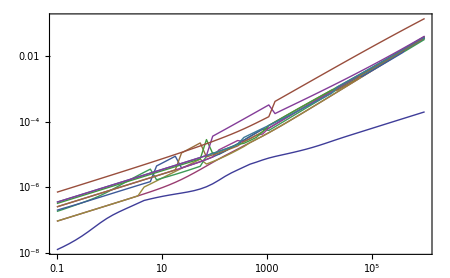

```mathematica
ListLogLogPlot[{Transpose@{f,Re[λ0[[All,1]]]},
Transpose@{f,Abs[λ0[[All,2]]]},
Transpose@{f,Abs[λ0[[All,3]]]},
Transpose@{f,Abs[λ0[[All,4]]]},
Transpose@{f,Abs[λ0[[All,5]]]},
Transpose@{f,Abs[λ0[[All,6]]]},
Transpose@{f,Abs[λ0[[All,7]]]},
Transpose@{f,Abs[λ0[[All,8]]]},
Transpose@{f,Abs[λ0[[All,9]]]},
Transpose@{f,Abs[λ0[[All,10]]]},
Transpose@{f,Abs[λ0[[All,11]]]}
},PlotRange-> All]
```

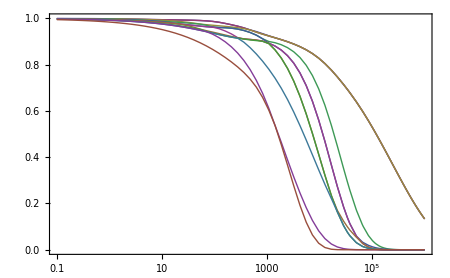

```mathematica
ListLogLinearPlot[{Transpose@{f,Abs[Am1[[All,1]]]},
Transpose@{f,Abs[Am1[[All,2]]]},
Transpose@{f,Abs[Am1[[All,3]]]},
Transpose@{f,Abs[Am1[[All,4]]]},
Transpose@{f,Abs[Am1[[All,5]]]},
Transpose@{f,Abs[Am1[[All,6]]]},
Transpose@{f,Abs[Am1[[All,7]]]},
Transpose@{f,Abs[Am1[[All,8]]]},
Transpose@{f,Abs[Am1[[All,9]]]},
Transpose@{f,Abs[Am1[[All,10]]]},
Transpose@{f,Abs[Am1[[All,11]]]}
},PlotRange-> All]
```